```mathematica
plandata={28.5,27.9,27.7,27.3,26.7};
convexdata={32.6,31.7,30.4,28.5,27.1};
```

```mathematica
rblende={10,16,24,32,40};
```

```mathematica
error=Sqrt[2]*0.1
```

0.141421

```mathematica
planDataProcessed=(plandata[[1]]-#&/@plandata)[[2;;]]
```

{0.6,0.8,1.2,1.8}

```mathematica
convexDataProcessed=(convexdata[[1]]-#&/@convexdata)[[2;;]]
```

{0.9,2.2,4.1,5.5}

```mathematica
(5.4+0.14)*5
```

27.7

```mathematica
28/5//N
```

5.6

```mathematica
rblendechopped=rblende[[2;;]]
```

{16,24,32,40}

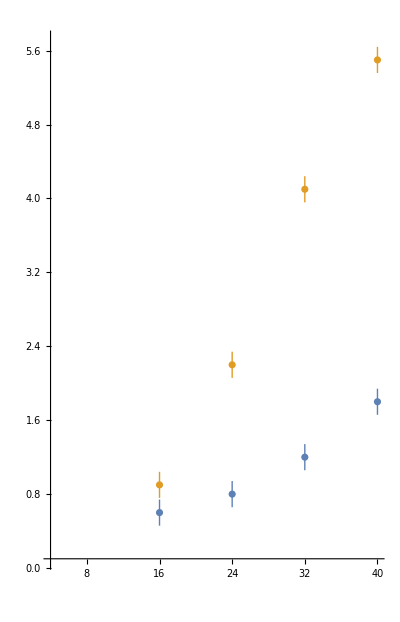

```mathematica
ListPlot[{Transpose[{rblendechopped,Around[#,error]&/@planDataProcessed}],Transpose[{rblendechopped,Around[#,error]&/@convexDataProcessed}]},PlotRange->{{4,40},{0.1,5.7}},AspectRatio->28/18]
```